```mathematica
receipts=Import["http://www.whatwepayfor.com/api/getReceiptAccount?year=2009","XML"];
```

```mathematica
expenses=Import["http://www.whatwepayfor.com/api/getBudgetAccount?income=100&showChange=1&showExtra=1&year=2009","XML"];
```

```mathematica
accountPairs={#[[1]],ToExpression[#[[2]]]}&/@Cases[expenses,XMLElement["item",{___,"account"->ac_,___,"amounti"->am_,___},___]->{ac,am},Infinity];
```

```mathematica
NetAccountAmount[indexes_]:=Total[accountPairs[[indexes,2]]];
```

```mathematica
ToBaseWord[w_]:=Block[{wn},wn=WordData[w];If[Length[wn]≤0,w,wn[[1,1]]]];
```

```mathematica
MeaningQ[w_]:=Block[{wn},wn=WordData[w,"PartsOfSpeech"];
NumberQ[w]
||(Not[MemberQ[wn,"Preposition"]]
&&Not[MemberQ[wn,"Conjunction"]]
&&Not[MemberQ[wn,"Determiner"]]
)
];
```

```mathematica
wordToAccountIds0=Flatten[Function[{accountIndex},{ToBaseWord[ToLowerCase[#]],accountIndex}&/@StringSplit[accountPairs[[accountIndex,1]],RegularExpression["[^a-zA-Z0-9]+"]]]/@Range[1,Length[accountPairs]],1];
wordToAccountIds=Select[{#[[1,1]],#[[All,2]]}&/@GatherBy[wordToAccountIds0,#[[1]]&],
MeaningQ[#[[1]]]&];
```

534

1557872000

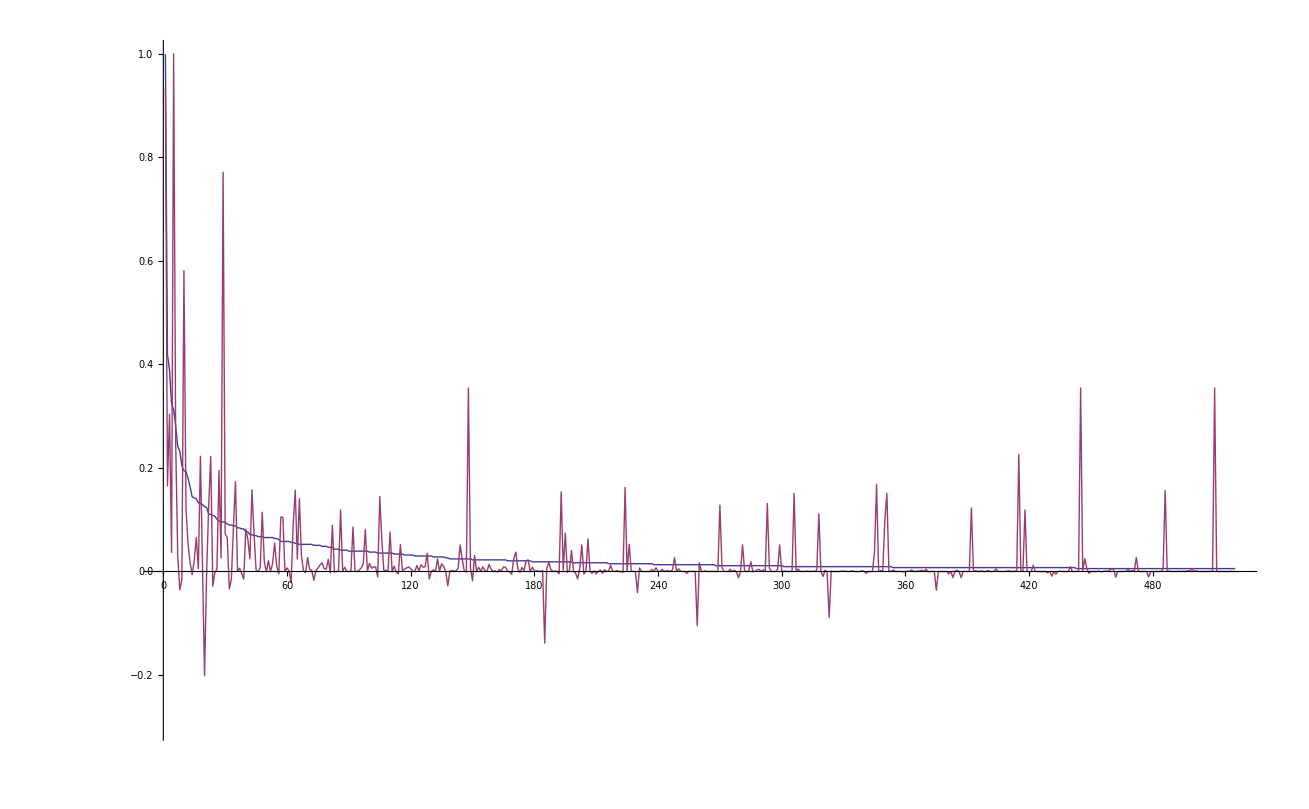

```mathematica
sum={#[[1]],Length[Union[#[[2]]]],NetAccountAmount[Union[#[[2]]]]}&/@wordToAccountIds;
maxCount=Max[sum[[All,2]]]
maxAmount=Max[sum[[All,3]]]
sum2={#[[1]],#[[2]],#[[3]],N[#[[2]]/maxCount],N[#[[3]]/maxAmount]}&/@sum;
TableForm[SortBy[sum2,(-#[[2]])&]];
ListLinePlot[{SortBy[sum2,(-#[[2]])&][[1;;520,4]],SortBy[sum2,(-#[[2]])&][[1;;520,5]]},PlotRange->{All,{-0.3,1}}]
```